## Mathematica for 1D propagation

```mathematica
SetDirectory["/Users/johnhawthorne/Desktop/Vahala_Research/SixSpinorJestadt/XProp4Spin/XPropFiles01022022"];
FileNames[]
```

{fort.100000,fort.100200,fort.100400,fort.100600,fort.100800,fort.101000,fort.101200,fort.101400,fort.101600,fort.101800,fort.102000,fort.102200,fort.102400,fort.102600,fort.102800,fort.103000,fort.103200,fort.103400,fort.103600,fort.103800,fort.104000,fort.104200,fort.104400,fort.104600,fort.104800,fort.105000,fort.105200,fort.105400,fort.105600,fort.105800,fort.106000,fort.106200,fort.106400,fort.106600,fort.106800,fort.107000,fort.107200,fort.107400,fort.107600,fort.107800,fort.108000,fort.108200,fort.108400,fort.108600,fort.108800,fort.109000,fort.109200,fort.109400,fort.109600,fort.109800,fort.110000,fort.110200,fort.110400,fort.110600,fort.110800,fort.111000,fort.111200,fort.111400,fort.111600,fort.111800,fort.112000,fort.112200,fort.112400,fort.112600,fort.112800,fort.113000,fort.113200,fort.113400,fort.113600,fort.113800,fort.114000,fort.114200,fort.114400,fort.114600,fort.114800,fort.115000,fort.115200,fort.115400,fort.115600,fort.115800,fort.116000,fort.600000,fort.600200,fort.600400,fort.600600,fort.600800,fort.601000,fort.601200,fort.601400,fort.601600,fort.601800,fort.602000,fort.602200,fort.602400,fort.602600,fort.602800,fort.603000,fort.603200,fort.603400,fort.603600,fort.603800,fort.604000,fort.604200,fort.604400,fort.604600,fort.604800,fort.605000,fort.605200,fort.605400,fort.605600,fort.605800,fort.606000,fort.606200,fort.606400,fort.606600,fort.606800,fort.607000,fort.607200,fort.607400,fort.607600,fort.607800,fort.608000,fort.608200,fort.608400,fort.608600,fort.608800,fort.609000,fort.609200,fort.609400,fort.609600,fort.609800,fort.610000,fort.610200,fort.610400,fort.610600,fort.610800,fort.611000,fort.611200,fort.611400,fort.611600,fort.611800,fort.612000,fort.612200,fort.612400,fort.612600,fort.612800,fort.613000,fort.613200,fort.613400,fort.613600,fort.613800,fort.614000,fort.614200,fort.614400,fort.614600,fort.614800,fort.615000,fort.615200,fort.615400,fort.615600,fort.615800,fort.616000,fort.9}

```mathematica
(* -------- PLOTTING FORTRAN OUTPUT ---------*)

ClearAll["Global`*"];
NumFiles=80;
stepSize=200;
Do[Ez[i*stepSize]=Import[StringJoin["fort.",ToString[600000+i*stepSize]],"Table" ];
psi1[i*stepSize]=Ez[i*stepSize],
{i,0,NumFiles}];
```

```mathematica
NumFiles=80;
stepSize=200;
Do[Bx[i*stepSize]=Import[StringJoin["fort.",ToString[100000+i*stepSize]],"Table" ];
psi2[i*stepSize]=Bx[i*stepSize],
{i,0,NumFiles}];
```

### Poytning Flux - time evolution

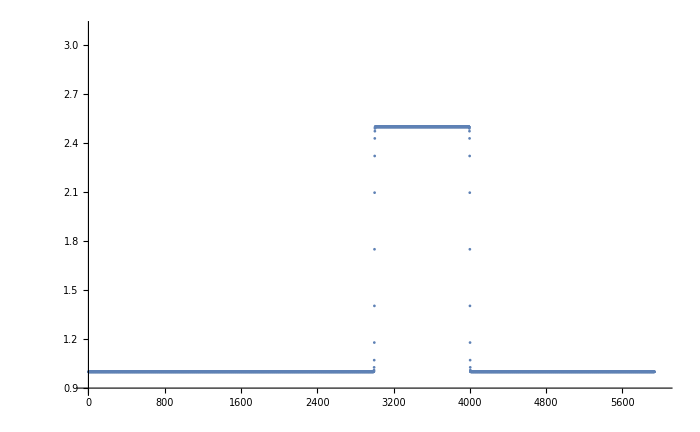

```mathematica
Poynt = Import["fort.9","Table"];ListPlot[Poynt,PlotRange->{{0,6000},{.9,3.1}},ImageSize->700]
```

```mathematica
(*  for 55k < t < 110k , the pulse is straddling the region of inhomogeneous dielectric region *)
```

### Ez, Bx - profiles

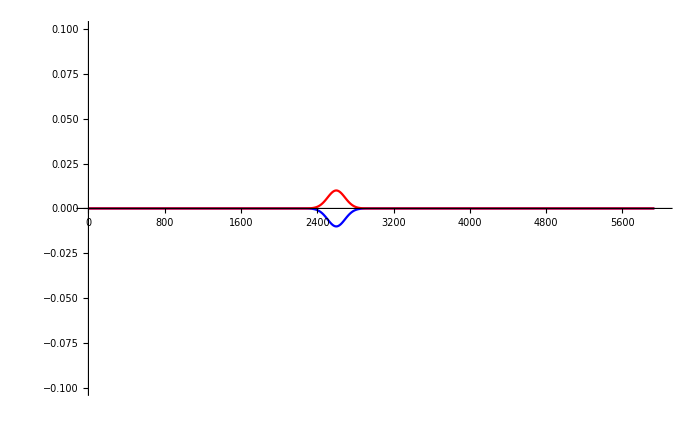

```mathematica
ListPlot[{psi1[1000],psi2[1000]},PlotRange->{{000,6000},{-0.1,0.1}},ImageSize->700,LabelStyle->Directive[FontSize->24],PlotStyle->{Blue,Red,Black,Green},Joined->True,FrameLabel->{"x"}]
```

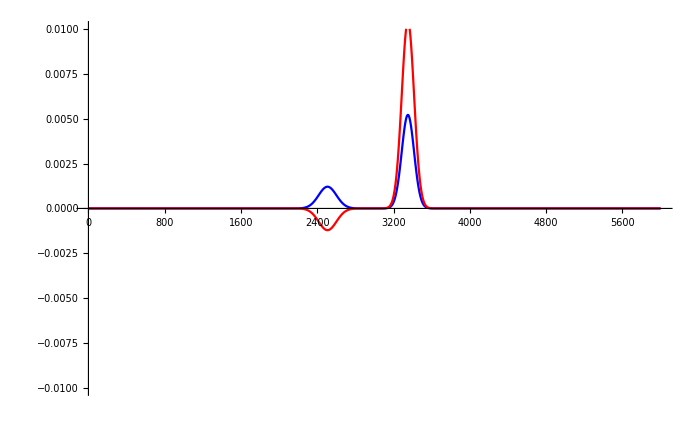

```mathematica
ListPlot[{Ez[5000],Bx[5000]},PlotRange->{{0,6000},{-0.01,0.01}},ImageSize->700,LabelStyle->Directive[FontSize->24],PlotStyle->{Blue,Red,Black,Green},Joined->True,FrameLabel->{"x"}]
```

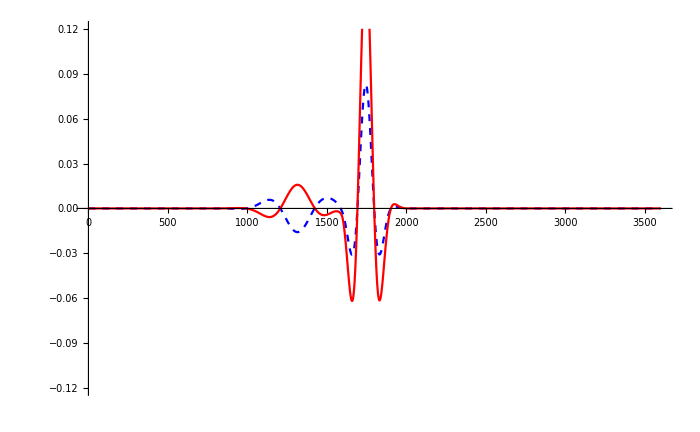

MaxValue::objfs: The objective function {0,0.000020773} should be scalar-valued.

MaxValue::ivar: 0 is not a valid variable. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/General/ivar",
ButtonNote->"MaxValue::ivar"]

```mathematica
ListPlot[{Ez[2400],Bx[2400]},PlotRange->{{0,3600},{-0.12,0.12}},ImageSize->700,LabelStyle->Directive[FontSize->24],PlotStyle->{{Blue,Dashed},Red,Black,Green},Joined->True,FrameLabel->{"x"}]
```

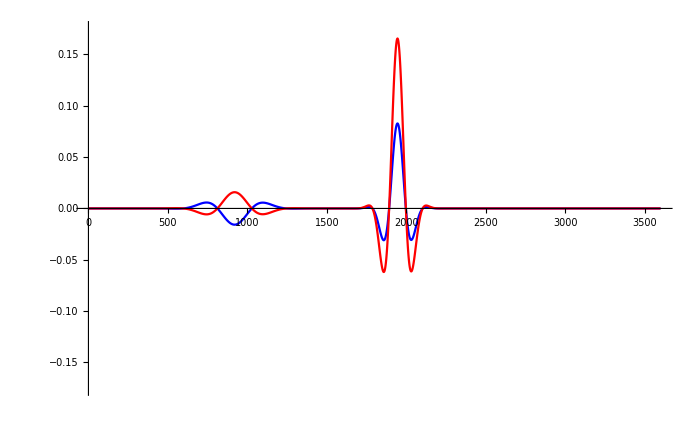

```mathematica
ListPlot[{Ez[3200],Bx[3200]},PlotRange->{{0,3600},{-0.175,0.175}},ImageSize->700,LabelStyle->Directive[FontSize->24],PlotStyle->{Blue,Red,Black,Green},Joined->True,FrameLabel->{"x"}]
```

```mathematica
ListPlot[{Ez[10800],Bx[10800]},PlotRange->{{0,2400},{-0.2751,0.2751}},ImageSize->700,LabelStyle->Directive[FontSize->24],PlotStyle->{{Blue,Dashed},Red,Black,Green},Joined->True,FrameLabel->{"x"}]
```

```mathematica
ListPlot[{Ez[116000],Bx[116000]},PlotRange->{{000,24000},{-0.21,0.21}},ImageSize->700,LabelStyle->Directive[FontSize->24],PlotStyle->{Blue,Red,Black,Green},Joined->True,FrameLabel->{"x"}]
```

```mathematica
ListPlot[{Ez[140000],Bx[140000]},PlotRange->{{0000,24000},{-0.3,0.3}},ImageSize->700,LabelStyle->Directive[FontSize->24],PlotStyle->{Blue,Red,Black,Green},Joined->True,FrameLabel->{"x"}]
```

```mathematica
ListPlot[{Ez[180000],Bx[180000]},PlotRange->{{0000,26000},{-0.21,0.21}},ImageSize->700,LabelStyle->Directive[FontSize->24],PlotStyle->{Blue,Red,Black,Green},Joined->True,FrameLabel->{"x"}]
```